# Interlude 1

## Calculus

## Section I1.1

### Exercise I1.1.1

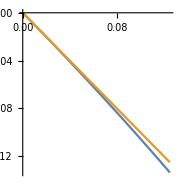
{-Graphics-,{-0.0606246,-0.0588235}}

```mathematica
With[{f=Log[1-#]&},
With[{
m=D[f[t],t]/.t->0,
b=f[0]
},
With[{g=m*#+b&},
{Plot[{f[t],g[t]},{t,0,1/8},
AspectRatio->Automatic,
ImageSize->Small
],
Through[{f,g}[1./17]]
}]]]
```

### Exercise I1.1.2

```mathematica
ClearAll[f,x,m,b];
```

```mathematica
f[x_]:=(1/4+x^2)^(1/2)
```

```mathematica
f[x]
```

√(1/4+x^2)

```mathematica
D[f[x],x]
```

x/(√(1/4+x^2))

```mathematica
m=%/.x->0
```

0

```mathematica
b=f[0]
```

1/2

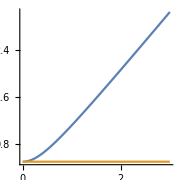

```mathematica
Plot[{f[x],m*x+b},{x,0,3},
PlotRange->{0,All},
AspectRatio->Automatic,
ImageSize->Small
]
```

```mathematica
ClearAll[f,x,m,b]
```

## Section I1.2

### Exercise I1.2.1

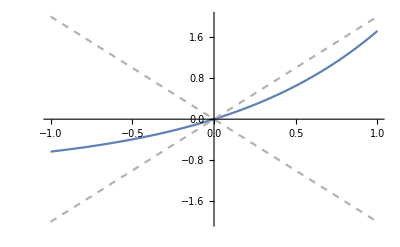

```mathematica
Plot[{Exp[x]-1,-2*x,2*x},{x,-1,1},
PlotStyle->{Automatic,
Directive[GrayLevel[0.7],Dashed],
Directive[GrayLevel[0.7],Dashed]}
]
```

```mathematica
Solve[Exp[x]-1==2*x,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0},{x→1/2 (-1-2 ProductLog[-1,-1/(2 √ⅇ)])}}

```mathematica
N[%]
```

{{x→0.},{x→1.25643}}

```mathematica
?ProductLog
```

ProductLog[z] gives the principal solution for w in z==w e^w. 
ProductLog[k,z] gives the k^th solution.

## Section I1.3

### Exercise I1.3.2

Sum[(k/n)^2 1/n.{k,n}]==1/n^3∑_k^n k^2==1/n^3(n^3/3+n^2/2+n/6)==1/3+1/(2n)+1/(6 n^2)==1/3+O(1/n)

### Exercise I1.3.4

Assuming

log(x)==∫_1^x 1/t ⅆt

Consider

log(x y)==∫_1^(x y) 1/t ⅆt==∫_1^x 1/t ⅆt+∫_x^(x y) 1/t ⅆt

For the second integral, change variables so that

t==u x

ⅆt==x ⅆu

∫_x^(x y) 1/t ⅆt==∫_1^y x/(u x)ⅆu==log(y)